# Non-trivial Equilibria Stability Analysis

## Finding Non-Trivial Equilibria & Plotting equilibria with prey birth rate (b) as control

```mathematica
(*Finding the equilibria system*)
ClearAll["Global`*"];
F[A_,B_]:=-dA*A+m*B+2*p*A*B
G[A_,B_]:=B*(-dB-m-2*p*A+2*b-2*b*(A+B))
M:={{Da*(1-B)+p*B,Da*A,0,0},{Db*B,Db*(1-A)-b*(A+B),0,0},{0,0,1,0},{0,0,0,1}};
(*Vector on the right-hand side*)
RHS = {-s*phi-F[A,B],-s*psi-G[A,B],phi,psi};
(*Isolating derivatives on the right hand-side {phiPrime,psiPrime,APrime,BPrime}*)
DynSis = Inverse[M].RHS;
(*Solve for derivatives when {phi',psi',A',B'}=0*)
EquilibriaEquation := DynSis == {0,0,0,0}
```

```mathematica
(*Solving the equilibia equations*)
equilibria = Solve[EquilibriaEquation, {phi, psi, A, B}];
(*Retrieving the 2 non-trivial equilibria points*)
NonTrivialEq = equilibria[[{2,3}]]; 
NonTrivialEq1 = equilibria[[2]];
```

```mathematica
EpsParameters = {Db -> ϵ,Da -> ϵ,D -> ϵ, dA -> ϵ^2, dB -> ϵ^2, m -> ϵ^3};
NumericalParameters = {Db -> 0.1, Da ->0.1, D->0.1, dA ->0.01, dB ->0.01,p->0.2, m -> 0.001};
```

```mathematica
(*Finding the equivalent non-trivial solutions with numerical parameters*)
NumA1[b_] := (A /. NonTrivialEq[[1]]) /. NumericalParameters;
EpsA1[b_] := (A /. NonTrivialEq[[1]]) /. EpsParameters;
NumB1[b_] := (B /. NonTrivialEq[[1]]) /. NumericalParameters;
EpsB1[b_] := (B /. NonTrivialEq[[1]]) /. EpsParameters;
Series[EpsA1[b],{ϵ,0,2}]
Series[EpsB1[b],{ϵ,0,2}]
(*These are not physically relevant, B2 is negative for whatever b parameter*)
NumA2[b_] := (A /. NonTrivialEq[[2]]) /. NumericalParameters;
EpsA2[b_] := (A /. NonTrivialEq[[2]]) /. EpsParameters;
NumB2[b_] := (B /. NonTrivialEq[[2]]) /. NumericalParameters;
EpsB2[b_] := (B /. NonTrivialEq[[2]]) /. EpsParameters;
```

(b p+√(b^2 p^2))/(2 p (b+p))-((b p+√(b^2 p^2)) ϵ^2)/(4 (b p^2))+O[ϵ]^3

(b p-√(b^2 p^2))/(2 b p)+((2 b-2 p+(2 √(b^2 p^2) (b+p))/(b p)) ϵ^2)/(8 b p)+O[ϵ]^3

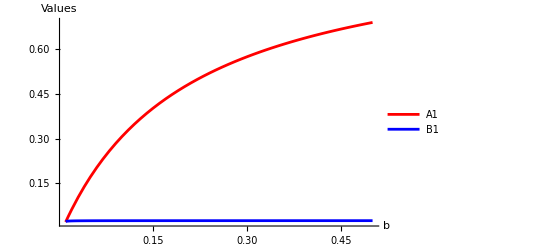

```mathematica
Plot[{NumA1[b], NumB1[b]}, {b, 0.01, 0.5},
     PlotLegends -> {"A1", "B1"},
     PlotStyle -> {Red, Blue},
     AxesLabel -> {"b", "Values"},
     PlotRange -> All]
```

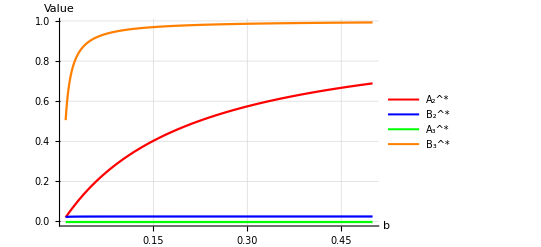

```mathematica
Plot[{NumA1[b], NumB1[b], NumA2[b], NumB2[b]}, {b, 0.01, 0.5},
	 PlotLegends -> {Style[Superscript[Subscript["A", "2"], "*"], Italic], Style[Superscript[Subscript["B", "2"], "*"], Italic], Style[Superscript[Subscript["A", "3"], "*"], Italic], Style[Superscript[Subscript["B", "3"], "*"],Italic]},
	 PlotStyle -> {
	   Directive[Red, Thickness[0.004]],
	   Directive[Blue, Thickness[0.004]],
	   Directive[Green, Thickness[0.004]],
	   Directive[Orange, Thickness[0.004]]
	   },
	 AxesLabel -> {Style["b",Italic], "Value"},
	 LabelStyle -> {FontSize -> 10},
	 GridLines -> Automatic,
	 PlotRange -> All
	 ]
```

To better understand which equilibria are physically relevant, one most

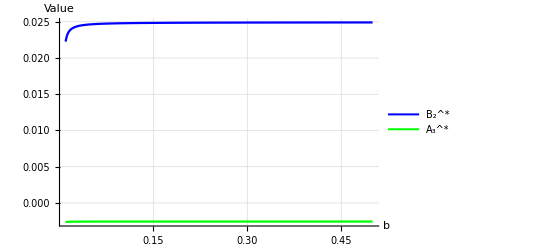

```mathematica
Plot[{NumB1[b],NumA2[b]}, {b, 0.01, 0.5},
     PlotLegends -> {Style[Superscript[Subscript["B", "2"], "*"], Italic],Style[Superscript[Subscript["A", "3"], "*"], Italic]},
     PlotStyle -> {
          Directive[Blue,Thickness[0.004]],
          Directive[Green, Thickness[0.004]]  
     },
     AxesLabel -> {Style["b",Italic], "Value"},
     LabelStyle->{FontSize -> 10},
     GridLines->Automatic,
     PlotRange -> All]
```

Here we note that the second equilibria, corresponding to  is not physically relevant as the quantity A2 is negative.

We now plot the rescaled system, considering the scaling B = ϵ ^2 B0

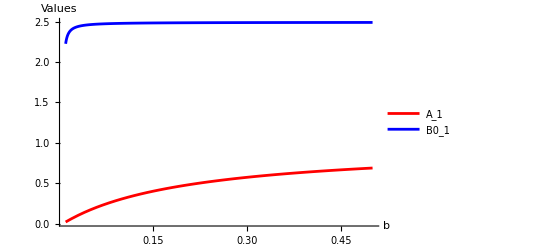

```mathematica
Clear[ϵ]
ϵ = 0.1;
Plot[{NumA1[b], NumB1[b]/ϵ^2}, {b, 0.01, 0.5},
     PlotLegends -> {"A_1", "B0_1"},
     PlotStyle -> {Red, Blue},
     AxesLabel -> {"b", "Values"},
     PlotRange -> All]
Clear[ϵ]
```

# Stability Analysis - Computation of the Jacobian & Eigenvalues

```mathematica
(*Jacobian computation & Evalutation At Equilibria*)
JacobianMatrix := D[DynSis,{{phi, psi, A, B}}];
JacAtEq1 := JacobianMatrix /. {phi -> 0, psi ->0, A -> NumA1[b], B -> NumB1[b]}
(*JacAtEq1 := JacobianMatrix /. {phi -> 0, psi ->0 , A -> BasicA1, B -> BasicB1};*)
JacAtEq2 = JacobianMatrix /. {phi -> 0, psi ->0, A -> A2[b], B -> B2[b]};
NumJacAtEq1 := JacAtEq1 /. NumericalParameters;
NumJacAtEq2 := JacAtEq2 /. NumericalParameters;
```

## Eigenvalues for Non-Trivial Equilibrium 1 (Predator prevails A1 =1, B1 = 0)

```mathematica
(*Makes a huge difference to hold all and first evaluate then afterwards just evaluate*)
(*Computing the numerical eigenvalues of the resulting numerical jacobian*)
ClearAll[NumEigAtEq1]
NumEigAtEq1 := Eigenvalues[NumJacAtEq1];
```

```mathematica
lightp = 0.4;
(*Control plot colours*)
SetOptions[$FrontEnd, PrintingStyleEnvironment -> "Working"];
commonOptsStability = {
   ColorFunction -> Function[{x, y, z}, 
        Which[z > 0, Lighter[Green, lightp], 
        z < 0, Lighter[Red, lightp], 
        True, Lighter[Yellow, lightp]]],
   ColorFunctionScaling -> False,
   MeshFunctions -> {#3 &},
   MeshStyle -> {{Thin, Black}},
   PlotRange -> {-5, 5},
   Ticks -> {Automatic, Automatic, Automatic},
   AxesLabel -> {"b", "s", "Re[eigen]"},
   Lighting -> "Neutral",
   Background -> White
};
SetOptions[$FrontEnd, PrintingStyleEnvironment -> "Working"];
commonOptsImaginary = {
   ColorFunction -> Function[{x, y, z}, 
        Which[z > 0, Lighter[Green, lightp], 
        z < 0, Lighter[Red, lightp], 
        True, Lighter[Yellow, lightp]]],
   MeshFunctions -> {#3 &},
   ColorFunctionScaling -> False,
   MeshStyle -> {{Thin, Black}},
   PlotRange -> {-5, 5},
   Ticks -> {Automatic, Automatic, Automatic},
   AxesLabel -> {"b", "s", "Im[eigen]"},
   Lighting -> "Neutral",
   Background -> White
};
```

```mathematica
Labeled[
		GraphicsGrid[{
			  {
			   Plot3D[Re[NumEigAtEq1[[1]]], {b, 0.01, 0.2}, {s, 0.04, 0.2},
			    PlotLabel -> Style["Eigenvalue 1", Italic, 11], Evaluate[commonOptsStability]],
			   
			   Plot3D[Re[NumEigAtEq1[[2]]], {b, 0.01, 0.2}, {s, 0.04, 0.2},
			    PlotLabel -> Style["Eigenvalue 2", Italic, 11], Evaluate[commonOptsStability]]
			   },
			  
			  {
			   Plot3D[Re[NumEigAtEq1[[3]]], {b, 0.01, 0.2}, {s, 0.04, 0.2},
			    PlotLabel -> Style["Eigenvalue 3", Italic, 11], Evaluate[commonOptsStability]],
			   
			   Plot3D[Re[NumEigAtEq1[[4]]], {b, 0.01, 0.2}, {s, 0.04, 0.2},
			    PlotLabel -> Style["Eigenvalue 4",Italic, 11], Evaluate[commonOptsStability]]
			   }
			  }
		]
		,
		Style[
		  Row[{
		    "Non-trivial Equilibrium Point: ",
		    Superscript[Subscript[X, 2], "*"]
		  }],
		  FontFamily -> "Helvetica",
		  12
		],
		Top
	]
```

-Graphics-Non-trivial Equilibrium Point: X_2^*

Density Map - Results are not that interesting

```mathematica
DensityPlot[
    {
      Re[NumEigAtEq1[[1]]],
      Re[NumEigAtEq1[[2]]],
      Re[NumEigAtEq1[[3]]],
      Re[NumEigAtEq1[[4]]]
    },
    {b, 0.01, 0.2}, {s, 0.04, 0.2},
    PlotLayout -> {"Row", 2},
    ColorFunction -> Function[{z},
      Which[
        z > 0.0, Green,
        z < 0.0, Red,
        True, Yellow
      ]
    ],
    ColorFunctionScaling -> False,
    PlotLegends -> Automatic
  ]
```

-Graphics-

```mathematica
Labeled[
		GraphicsGrid[{
			  {
			   Plot3D[Im[NumEigAtEq1[[1]]], {b, 0.01, 0.2}, {s, 0.04, 0.2},
			    PlotLabel -> Style["Eigenvalue 1", Italic, 11], Evaluate[commonOptsImaginary]],
			   
			   Plot3D[Im[NumEigAtEq1[[2]]], {b, 0.01, 0.2}, {s, 0.04, 0.2},
			    PlotLabel -> Style["Eigenvalue 2", Italic, 11], Evaluate[commonOptsImaginary]]
			   },
			  
			  {
			   Plot3D[Im[NumEigAtEq1[[3]]], {b, 0.01, 0.2}, {s, 0.04, 0.2},
			    PlotLabel -> Style["Eigenvalue 3", Italic, 11], Evaluate[commonOptsImaginary]],
			   
			   Plot3D[Im[NumEigAtEq1[[4]]], {b, 0.01, 0.2}, {s, 0.04, 0.2},
			    PlotLabel -> Style["Eigenvalue 4",Italic, 11], Evaluate[commonOptsImaginary]]
			   }
			  }
		]
		,
		Style[
		  Row[{
		    "Non-trivial Equilibrium Point: ",
		    Superscript[Subscript[X, 2], "*"]
		  }],
		  FontFamily -> "Helvetica",
		  12
		],
		Top
	]
```

-Graphics-Non-trivial Equilibrium Point: X_2^*

```mathematica
DensityPlot[
    {
      Im[NumEigAtEq1[[1]]],
      Im[NumEigAtEq1[[2]]],
      Im[NumEigAtEq1[[3]]],
      Im[NumEigAtEq1[[4]]]
    },
    {b, 0.01, 0.2}, {s, 0.04, 0.2},
    PlotLayout -> {"Row", 2},
    ColorFunction -> Function[{z},
      Which[
        z > 0.0, Green,
        z < 0.0, Red,
        True, Yellow
      ]
    ],
    ColorFunctionScaling -> False,
    PlotLegends -> Automatic
  ]
```

-Graphics-